## Get the Data

### Import data from files

```mathematica
(*wordsworthFiles = FileNames["*","/Users/verbal/desktop/projects/apps/local/rhymetrix/data/poetry-collection-api/collection/William Wordsworth/"];*)
```

```mathematica
(*FileNames["*","/Users/verbal/desktop/projects/apps/local/rhymetrix/data/poetry-collection-api/collection/William Wordsworth/"];*)
```

```mathematica
allAuthors= FileNames["*","/Users/verbal/desktop/projects/apps/local/rhymetrix/data/poetry-collection-api/collection/"];
```

```mathematica
allPoemFiles = FileNames["*",Table[allAuthors[[i]],{i,1,Length[allAuthors]}]]
```

{/Users/verbal/desktop/projects/apps/local/rhymetrix/data/poetry-collection-api/collection/A. A. Milne/Disobedience.json,/Users/verbal/desktop/projects/apps/local/rhymetrix/data/poetry-collection-api/collection/A. A. Milne/Forgotten.json,12526,/Users/verbal/desktop/projects/apps/local/rhymetrix/data/poetry-collection-api/collection/Zozan Hawez/Self-Portrait.json}
 |  |  |  |

```mathematica
samplePoemFiles = RandomSample[allPoemFiles,2000];
```

### Get poem lines (List of List of Lists)

```mathematica
allPoems = Table[StringSplit[Import[samplePoemFiles[[i]], "RawJSON"]["text"]],{i,Length[samplePoemFiles]}](* Let's just use 100 *)
```

{{{I,take,my,dinners,alone,},{in,my,room,,but,I,can,still},{hear,them,through,the,door,},{my,father’s,false,teeth},{clicking,like,a,wooden,gate},{with,a,metal,latch,,swinging},40,{A,faraway,splash,in,the,middle},{of,the,night,,I,sit,up,in,bed,,startled—},{it,was,George,Washington,throwing},{something,across,the,Delaware,},{not,a,coin,,but,his,teeth.}},1998,{1}}
 |  |  |  |

## Prepare The Data

### Support Functions

Func to create different sized windows from list of list of poems last words

```mathematica
createWinLists[a_,winSize_] := MovingMap[List,a,winSize]
```

Func to create pairs from list of word lists: Pairing procedure is n1(n2...nX)

```mathematica
createWinPairs[a_] := Table[{a[[1]],a[[i]]},{i,2,Length[a]}]
```

Func to sort pairs alphabetically for consistency in comparing pairs like {trouble,bubble} vs {bubble,trouble}

```mathematica
alphaSortPairs[a_] := Table[Sort[a[[i]]],{i,1,Length[a]}]
```

Func to trim normal and weird whitespaces

```mathematica
myStringTrim[a_] := ToString[StringTrim[a,(".97"|" ")]]
```

### Get Last Word Lists From Rhyming Poem(s)

```mathematica
allPoems
```

{{{James,James},{Morrison,Morrison},{Weatherby,George,Dupree},{Took,great},{Care,of,his,Mother,},{Though,he,was,only,three.},{James,James},{Said,to,his,Mother,},54,{Took,great},{C/o,his,M*****},{Though,he,was,only,3.},{J.,J.},{Said,to,his,M*****},{“M*****,”,he,said,,said,he:},{“You-must-never-go-down-to-the-end-of-the-town-},{if-you-don’﻿t-go-down-with,ME!”}},{1},496,{1},{1}}
 |  |  |  |

#### Isolate Last Words and Strip Out Punctuation

```mathematica
poemslastwords = Table[StringReplace[allPoems[[i]][[All, -1]], PunctuationCharacter:>""],{i,Length[allPoems]}]
```

{{alone,still,door,teeth,gate,swinging,closed,night,exhibit,formaldehyde,child,shining,glass,flashlight,cave,fossilized,bird,fathers,tries,in,enough,underwater,them,pipe,wedged,open,expels,something,teeth,Washington,alone,wood,ivory,Gods,wings,hooves,together,bones,fly,teeth,keys,eucalyptus,window,skin,pavement,parchment,middle,startled,throwing,Delaware,teeth},1998,{last,withheld,birds,pupils,scaffolds,entered,spills,uncovered,trespass,,51,mind,reins,stops,out,plume,everything,nail,tail,vanishing,things}}
 |  |  |  |

### Create Lists from poems last words with a window size of 3

```mathematica
windowedLastWords = Table[createWinLists[poemslastwords[[i]],3],{i,1,Length[allPoems]}];
```

#### Create Pairs from Windowed Lists - Flatten and Reshape

```mathematica
allFlat = Flatten[Map[createWinPairs,windowedLastWords,{3}]]
```

{alone,still,alone,door,alone,teeth,still,door,still,teeth,still,gate,door,teeth,door,gate,door,swinging,teeth,gate,teeth,swinging,teeth,closed,gate,swinging,gate,closed,gate,night,443410,stops,out,stops,plume,stops,everything,out,plume,out,everything,out,nail,plume,everything,plume,nail,plume,tail,everything,nail,everything,tail,everything,vanishing,nail,tail,nail,vanishing,nail,things}
 |  |  |  |

```mathematica
windowedLastWordPairs = ArrayReshape[allFlat,{Divide[Length[allFlat[[;;-1]]],2],2}]
```

{{alone,still},{alone,door},{alone,teeth},{still,door},{still,teeth},{still,gate},{door,teeth},{door,gate},{door,swinging},{teeth,gate},{teeth,swinging},{teeth,closed},{gate,swinging},{gate,closed},{gate,night},{swinging,closed},{swinging,night},221701,{reins,out},{reins,plume},{stops,out},{stops,plume},{stops,everything},{out,plume},{out,everything},{out,nail},{plume,everything},{plume,nail},{plume,tail},{everything,nail},{everything,tail},{everything,vanishing},{nail,tail},{nail,vanishing},{nail,things}}
 |  |  |  |

#### Alphabetize Pair Lists

```mathematica
windowedAlphaLastWordPairs = alphaSortPairs[windowedLastWordPairs];
```

#### Lists to Rules

```mathematica
windowedAlphaLastWordPairRules = Apply[Rule,windowedAlphaLastWordPairs,{1}];
```

Sorted for easy viewing

```mathematica
orderedCountsWindowPairs = Sort[Map[Counts,{windowedAlphaLastWordPairRules}][[1]],Greater]
```

<|(→)→430,(me→me)→64,(light→night)→55,(you→you)→55,(it→it)→54,(→you)→50,(→the)→43,(away→day)→43,(→it)→40,(→me)→39,(day→way)→37,(breath→death)→35,(down→town)→34,(me→see)→34,(be→me)→33,(life→lost)→32,(→something)→30,150910,(closed→exhibit)→1,(exhibit→swinging)→1,(night→swinging)→1,(closed→swinging)→1,(gate→night)→1,(closed→gate)→1,(gate→swinging)→1,(closed→teeth)→1,(swinging→teeth)→1,(gate→teeth)→1,(door→swinging)→1,(door→gate)→1,(door→teeth)→1,(gate→still)→1,(still→teeth)→1,(door→still)→1,(alone→still)→1|>
 |  |  |  |

## Explore Pairs

### 3-Window Pairs - Baseline

Graph of 3-Window Pairs in dataset

```mathematica
nWindowPairsGraph = UndirectedGraph[windowedAlphaLastWordPairRules];
```

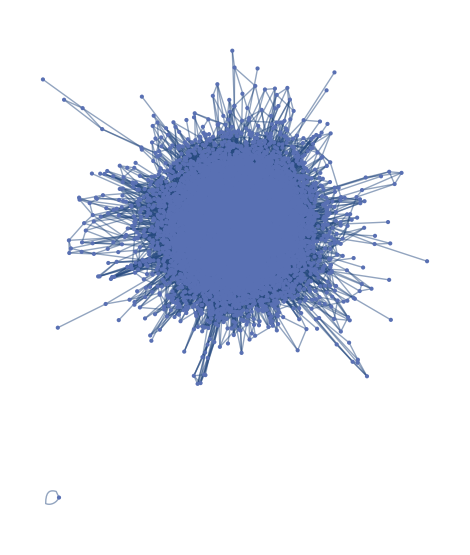

```mathematica
nWindowPairsGraph
```

### Gather Relevant Info from Baseline Graph

```mathematica
nWindowPairsGraphVerts = VertexList[nWindowPairsGraph];
nWindowPairsGraphVertsDegree = VertexDegree[nWindowPairsGraph];
nodeVertexDegrees = Thread[nWindowPairsGraphVerts -> nWindowPairsGraphVertsDegree];
{orderedPairs,orderedPairsCounts}=Transpose@KeyValueMap[List,orderedCountsWindowPairs];
```

Plot Repeated Word Pair Count in Log Space

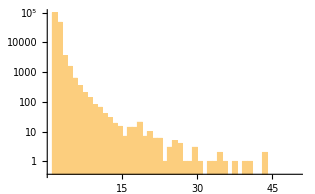

```mathematica
Histogram[orderedCountsWindowPairs,{1,50,1},"LogCount"]
```

Plot of Count of Vertex Connections in Log Space

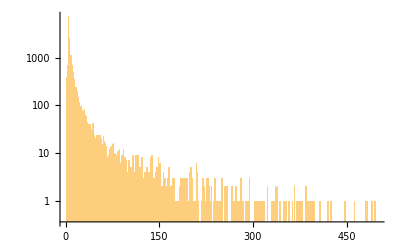

```mathematica
Histogram[VertexDegree[nWindowPairsGraph],{1,500,1},"LogCount"]
```

```mathematica
N@Mean@VertexDegree[nWindowPairsGraph]
```

13.1069

Explore Neighborhood of a given vertex

## Prepare Edge Weights and Threshold (add terminal ortho identity bonus)

### Calculate Edge Weights

```mathematica
orderedPairsCountsDenom1 = Monitor[Table[Lookup[nodeVertexDegrees,orderedPairs[[All,1]][[i]]],{i,Length[orderedPairs]}],i];
```

```mathematica
orderedPairsCountsDenom2 = Monitor[Table[Lookup[nodeVertexDegrees,orderedPairs[[All,2]][[i]]],{i,Length[orderedPairs]}],i];
```

```mathematica
weights1 = 1/ Thread[orderedPairsCounts/(orderedPairsCountsDenom1 + orderedPairsCountsDenom2)]
weights2 = 1/ Thread[orderedPairsCounts/(Sqrt[(orderedPairsCountsDenom1) + (orderedPairsCountsDenom2)])]
```

{705/34,451/48,562/41,649/27,402/13,28/5,115/12,265/12,542/11,24,37/3,451/21,527/20,731/19,454/19,355/19,371/19,21,5/3,234/17,97/8,67/4,44/15,31/5,406/15,1108/15,52/3,761/15,108/7,123/7,285/7,2,204/7,27,299/14,211/7,17/7,199/13,361/13,62/13,303/13,185/13,450/13,339/13,19,870/13,79/13,296/13,1076/13,825/13,358/13,83/3,719/12,253/6,77/2,39/2,164/3,367/12,131/6,301/12,59/6,18,49846,85,34,12,15,34,15,34,12,34,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,18,18,18,22,22,28,28,34,38,96,100,106,79,85,60,101,91,107,565,115,41,76,101,18,43,68,47,72,14,33}
 |  |  |  |

{(√(705/2))/34,(√451)/48,(√562)/41,(√649)/27,(√201)/13,(2 √(7/5))/5,(√(115/2))/12,(√(265/2))/12,(√271)/11,2 √(3/11),(√(37/7))/3,(√451)/21,(√527)/20,(√731)/19,(√454)/19,(√355)/19,(√371)/19,√(7/6),(√(5/6))/3,(3 √26)/17,(√(97/2))/8,(√67)/8,(2 √11)/15,(√(31/3))/5,(√406)/15,(2 √277)/15,(2 √(13/5))/3,(√761)/15,(3 √6)/7,(√(123/2))/7,(√(285/2))/7,1/(√7),(√102)/7,3 √(3/14),(√299)/14,(√(211/2))/7,(√(17/2))/7,(√199)/13,19/13,(√62)/13,(√303)/13,(√185)/13,(15 √2)/13,(√339)/13,√(19/13),(√870)/13,(√79)/13,(2 √74)/13,(2 √269)/13,(5 √33)/13,(√358)/13,(√83)/6,49866,2 √3,2 √3,2 √3,2 √3,2 √3,2 √3,2 √3,2 √3,2 √3,2 √3,2 √3,2 √3,2 √3,2 √3,2 √3,2 √3,2 √3,2 √3,2 √3,2 √3,2 √3,2 √3,3 √2,3 √2,3 √2,√22,√22,2 √7,2 √7,√34,√38,4 √6,10,√106,√79,√85,2 √15,√101,√91,√107,√565,√115,√41,2 √19,√101,3 √2,√43,2 √17,√47,6 √2,√14,√33}
 |  |  |  |

### Set Graph Trimming Threshold

```mathematica
Mean[weights2];
```

```mathematica
threshold = Mean[orderedPairsCounts]*3
```

44943/9994

```mathematica
threshold2 = Median[weights2];
```

2 √13

## Trim Graph

### Trimmed Graph 1

```mathematica
orderedPairsCounts
```

{430,64,55,55,54,50,43,43,40,39,37,35,34,34,33,32,30,29,29,29,28,27,26,26,26,26,25,25,25,25,25,24,24,24,23,22,22,22,22,22,22,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,150741,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}
 |  |  |  |

```mathematica
cutGraph = Monitor[Table[If[orderedPairsCounts[[i]]≥threshold,orderedPairs[[i]]->orderedPairsCounts[[i]],##&[]],{i,1,Length[orderedPairs]}],i];
```

```mathematica
cutGraph
```

```mathematica
Sort[cutGraph,Greater];
```

```mathematica
cutOrderedPairs = Table[cutGraph[[i]][[1]],{i,1,Length[cutGraph]}];
```

```mathematica
cutOrderedPairsCounts= Table[cutGraph[[i]][[2]],{i,1,Length[cutGraph]}];
```

```mathematica
cutOrderedPairsCountsInverse = 1/cutOrderedPairsCounts ;
```

### Trimmed Graph 2

```mathematica
cutGraph2 = Monitor[Table[If[N[weights1[[i]]]≤10,orderedPairs[[i]]->orderedPairsCounts[[i]],##&[]],{i,1,Length[orderedPairs]}],i];
```

```mathematica
cutOrderedPairs2 = Monitor[Table[cutGraph2[[i]][[1]],{i,1,Length[cutGraph2]}],i];
```

```mathematica
Length[cutGraph2]
```

3262

```mathematica
Sort[cutGraph2,Greater]
```

{(breath→death)→48,(like→like)→25,(Alraschid→time)→24,(cetera→cetera)→18,(London→London)→15,(forlorn→morn)→15,(aweary→dreary)→14,(Jane→What)→14,(Alraschid→prime)→13,(like→Like)→13,(tonight→tonight)→12,(follow→forget)→10,(dislike→like)→10,(nitrogen→translation)→9,(mere→wonderful)→8,(arm→wonderful)→8,(heaven→seven)→8,(Kashmir→Kashmir)→8,(Kashmir→universe)→8,(fools→rules)→8,(James→Mother)→8,(reposes→roses)→7,(elephants→Kashmir)→7,(Delaware→Delaware)→6,(London→wonderland)→6,(changes→ranges)→6,3210,(enlightenment→spent)→1,(dignity→inequality)→1,(inequality→squarecut)→1,(difference→objectivity)→1,(unafraid→undatable)→1,(original→undatable)→1,(contradictory→multiply)→1,(banjo→canals)→1,(orderlies→ramps)→1,(bluegrass→outskirts)→1,(halfbent→slowdrag)→1,(slowdrag→slur)→1,(Lincoln→When)→1,(Lincoln→pen)→1,(Astor→shudder)→1,(disaster→shudder)→1,(Astor→disaster)→1,(﻿﻿→liver)→1,(Sees→terrified)→1,(﻿a→eyrie)→1,(ferocity→vigils)→1,(vats→vigils)→1,(MovingMap[List,{{},{}},3]→MovingMap[List,{{},{}},3])→1,(BUT→darling)→1,(jaws→paws)→1,(paws→wrap)→1}
 |  |  |  |

```mathematica
cutOrderedPairsCounts2= Table[cutGraph2[[i]][[2]],{i,1,Length[cutGraph2]}];
```

```mathematica
cutOrderedPairsCountsInverse2 = 1/cutOrderedPairsCounts2 ;
```

```mathematica
cutOrderedPairsCountsInverse2
```

{1/10,1/8,1/8,1/8,1/7,1/7,1/7,1/6,1/6,1/6,1/6,1/6,1/6,1/6,1/6,1/6,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,17354,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}
 |  |  |  |

## Since we do not yet have proper performance metrics, here are some graphs on a small enough random sample of our data that we can easily visualize.

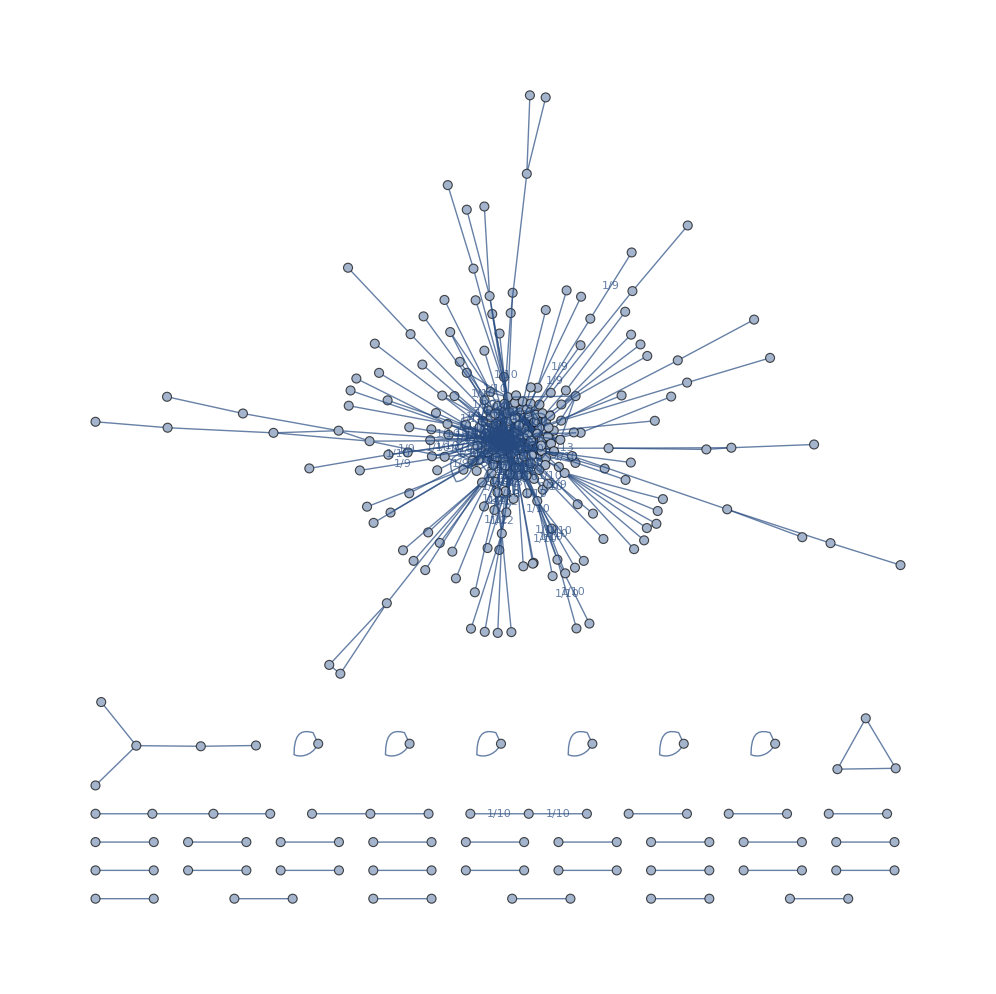

```mathematica
weightedTrimmedGraph =UndirectedGraph[cutOrderedPairs,EdgeWeight-> cutOrderedPairsCountsInverse,EdgeLabels->"EdgeWeight", VertexLabels-> "Name",GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True}]
```

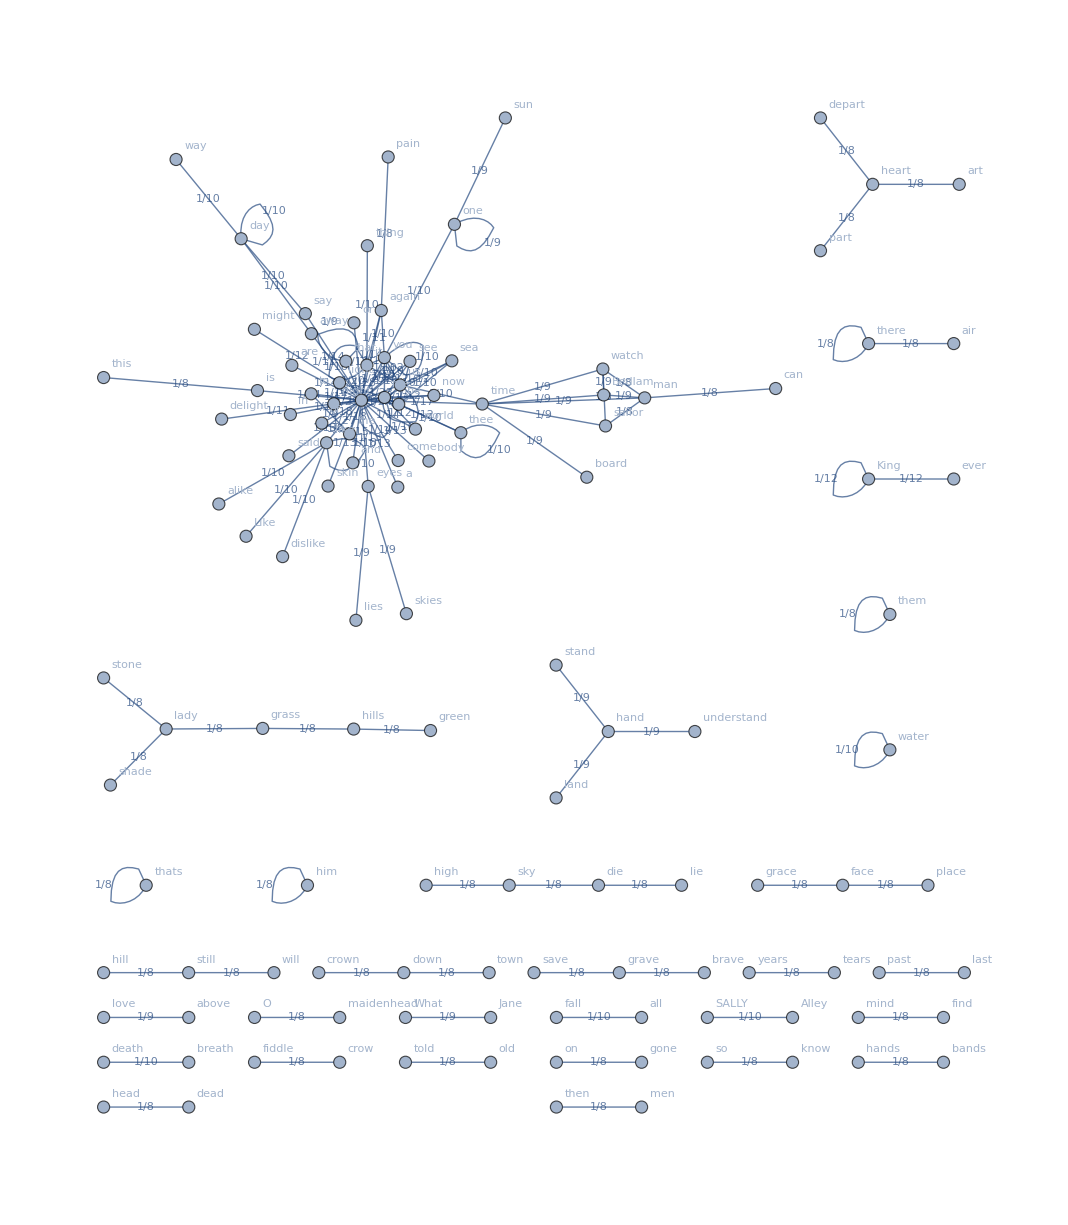

```mathematica
weightedTrimmedGraph =UndirectedGraph[cutOrderedPairs,EdgeWeight-> cutOrderedPairsCountsInverse,EdgeLabels->"EdgeWeight", VertexLabels-> "Name",GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True}]
```

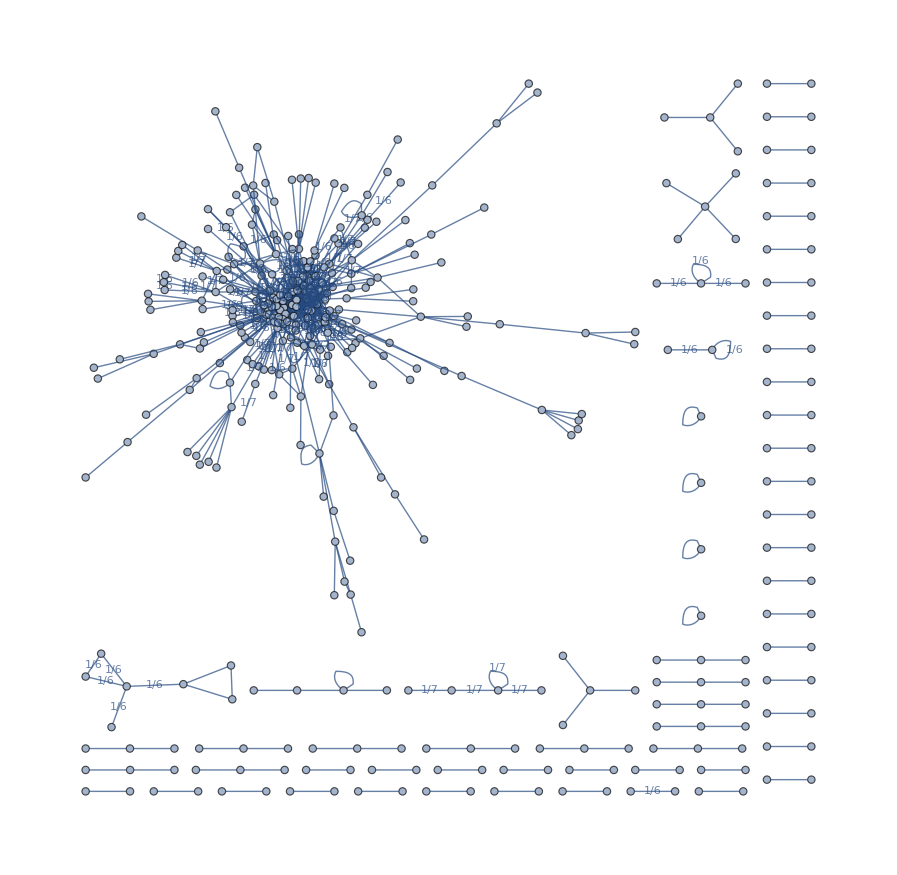

```mathematica
weightedTrimmedGraph =UndirectedGraph[cutOrderedPairs,EdgeWeight-> cutOrderedPairsCountsInverse,EdgeLabels->"EdgeWeight", VertexLabels-> "Name",GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True}]
```

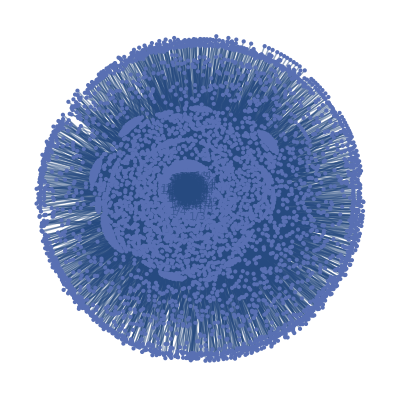

```mathematica
weightedTrimmedGraph2 =UndirectedGraph[cutOrderedPairs2,EdgeWeight-> cutOrderedPairsCountsInverse2,EdgeLabels->"EdgeWeight", VertexLabels-> "Name",GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True}]
```

## Explore Graphs at Neighborhood Level

#### Unweighted Graph

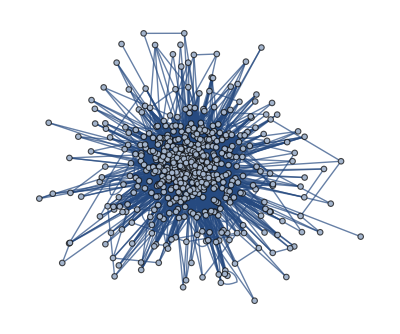

```mathematica
x := RandomSample[VertexList[nWindowPairsGraph],1]
NeighborhoodGraph[nWindowPairsGraph,"sky"] 
(*NeighborhoodGraph[nWindowPairsGraph,a=x]*)
a[[1]]
```

#### Weighted & Trimmed Graph

```mathematica
y := RandomSample[VertexList[weightedTrimmedGraph],1]
```

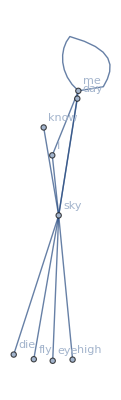

```mathematica
NeighborhoodGraph[weightedTrimmedGraph,"sky",VertexLabels->"Name"]
```

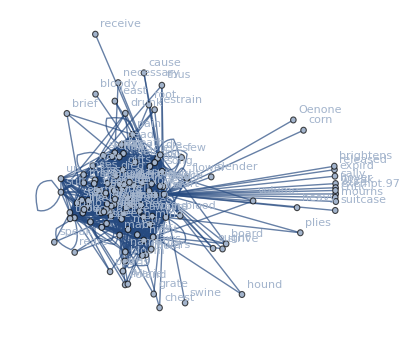

{clay}

```mathematica
NeighborhoodGraph[weightedTrimmedGraph2,"heart", VertexLabels->"Name"]
b[[1]]
```

```mathematica
gWeighted3 = UndirectedGraph[cutOrderedPairs2,EdgeWeight-> cutOrderedPairsCountsInverse2,EdgeLabels->"EdgeWeight", VertexLabels-> "Name",GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True}]
```

$Aborted[]

```mathematica
NeighborhoodGraph[weightedTrimmedGraph,"roam", VertexLabels->"Name",GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True}]
```

```mathematica
gWeighted1 = UndirectedGraph[orderedPairs,EdgeWeight-> orderedPairsCounts]
```

-Graphics-

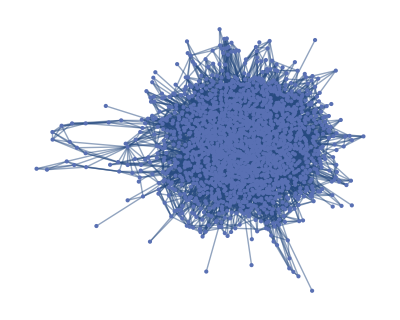

```mathematica
gWeighted1a = UndirectedGraph[gWeighted1]
```

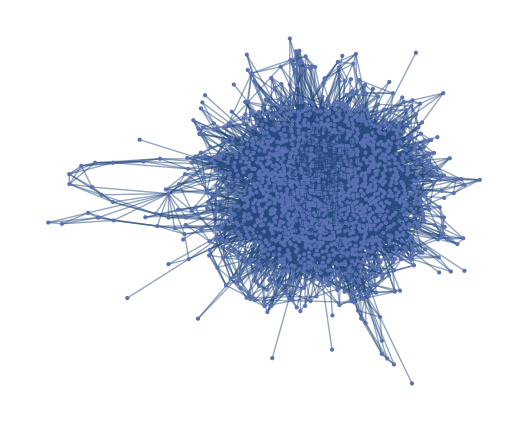

```mathematica
gWeighted2 = UndirectedGraph[gWeighted2,EdgeWeight-> orderedPairsCounts]
```

```mathematica
orderedCountsWindowPairs
```

<|(→)→430,(me→me)→64,(light→night)→55,(you→you)→55,(it→it)→54,(→you)→50,(→the)→43,(away→day)→43,(→it)→40,(→me)→39,(day→way)→37,(breath→death)→35,(down→town)→34,(me→see)→34,(be→me)→33,(life→lost)→32,(→something)→30,150910,(closed→exhibit)→1,(exhibit→swinging)→1,(night→swinging)→1,(closed→swinging)→1,(gate→night)→1,(closed→gate)→1,(gate→swinging)→1,(closed→teeth)→1,(swinging→teeth)→1,(gate→teeth)→1,(door→swinging)→1,(door→gate)→1,(door→teeth)→1,(gate→still)→1,(still→teeth)→1,(door→still)→1,(alone→still)→1|>
 |  |  |  |

```mathematica
testGraph = NeighborhoodGraph[gWeighted1a,{"strife"}, VertexLabels->"Name", GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True}]
```

```mathematica
Graph[e,EdgeWeight->w,EdgeLabelStyle->Directive[Red,20,Background->White],EdgeLabels->el,EdgeShapeFunction->el/.{((a_->b_)->c_)->((a->b)->({AbsoluteThickness[.9+c/4],Arrow[#1,0.025]}&))}]
```

```mathematica
GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True}
```

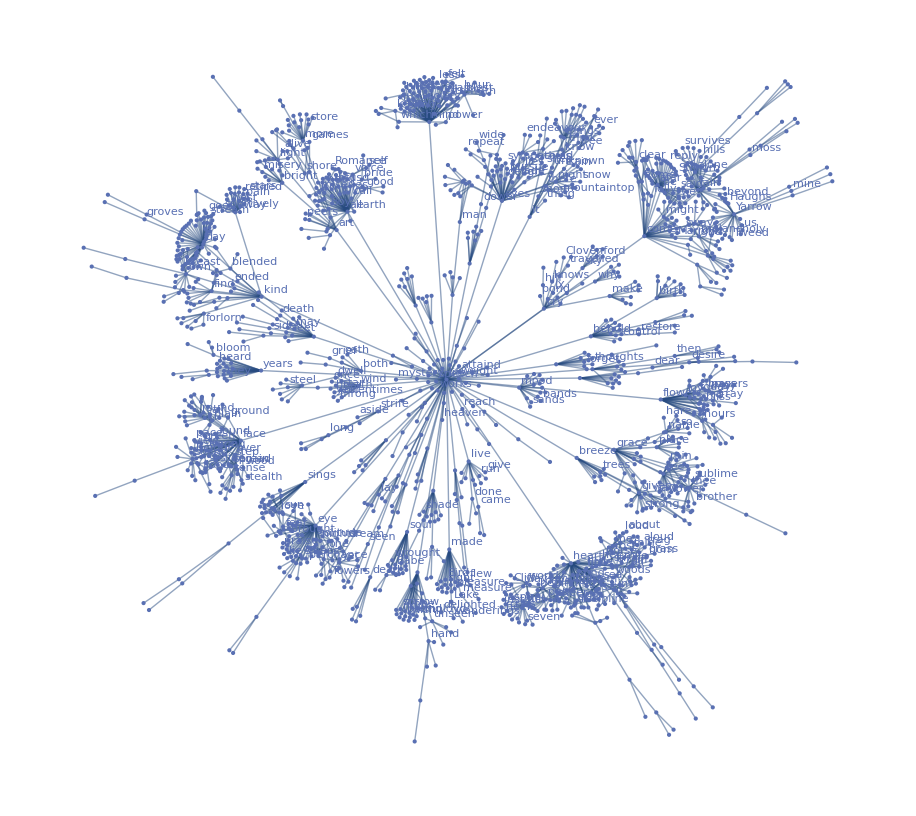

```mathematica
gSpanTree = FindSpanningTree[gWeighted1a, VertexLabels-> "Name"]
```

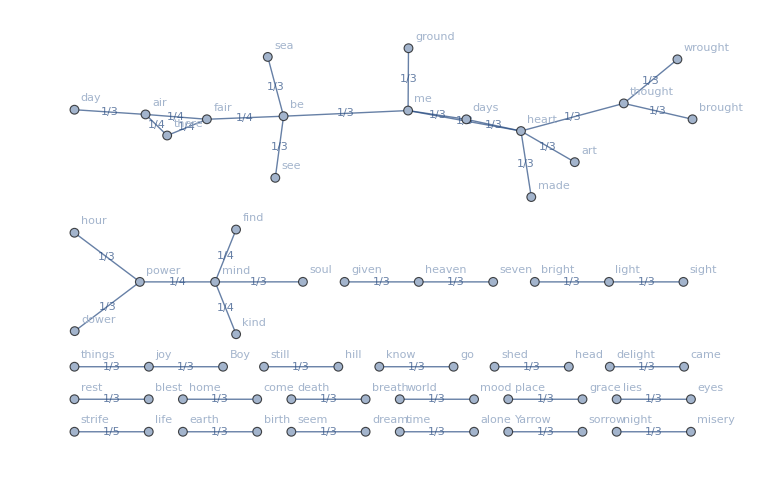

```mathematica
gWeighted3 = UndirectedGraph[cutOrderedPairs,EdgeWeight-> cutOrderedPairsCountsInverse,EdgeLabels->"EdgeWeight", VertexLabels-> "Name",GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True}]
```

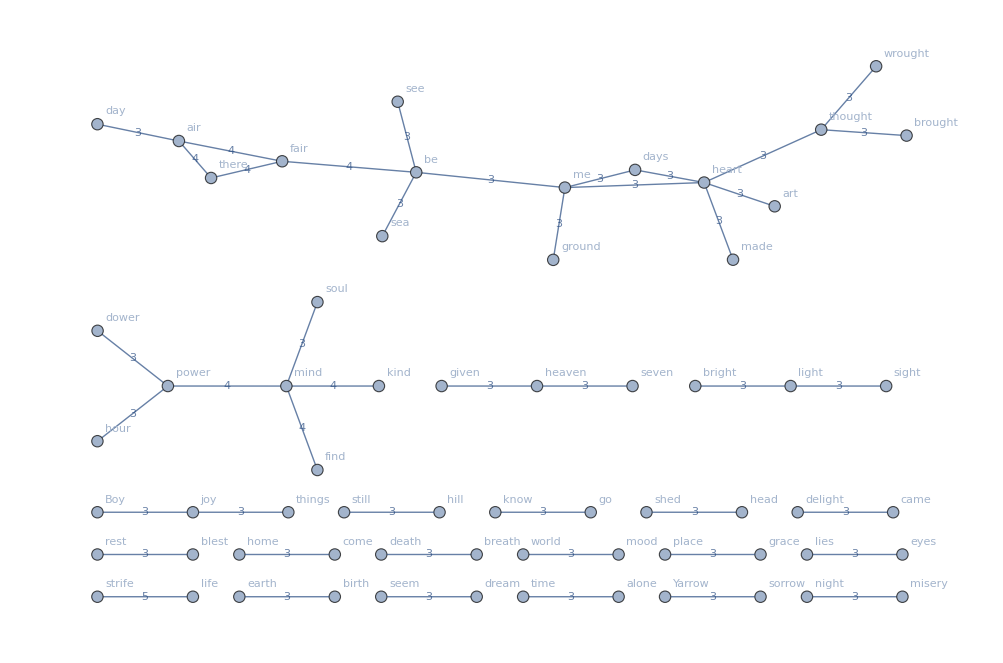

```mathematica
gWeighted4 = UndirectedGraph[cutOrderedPairs,EdgeWeight-> cutOrderedPairsCounts,EdgeLabels->"EdgeWeight", VertexLabels-> "Name"]
```

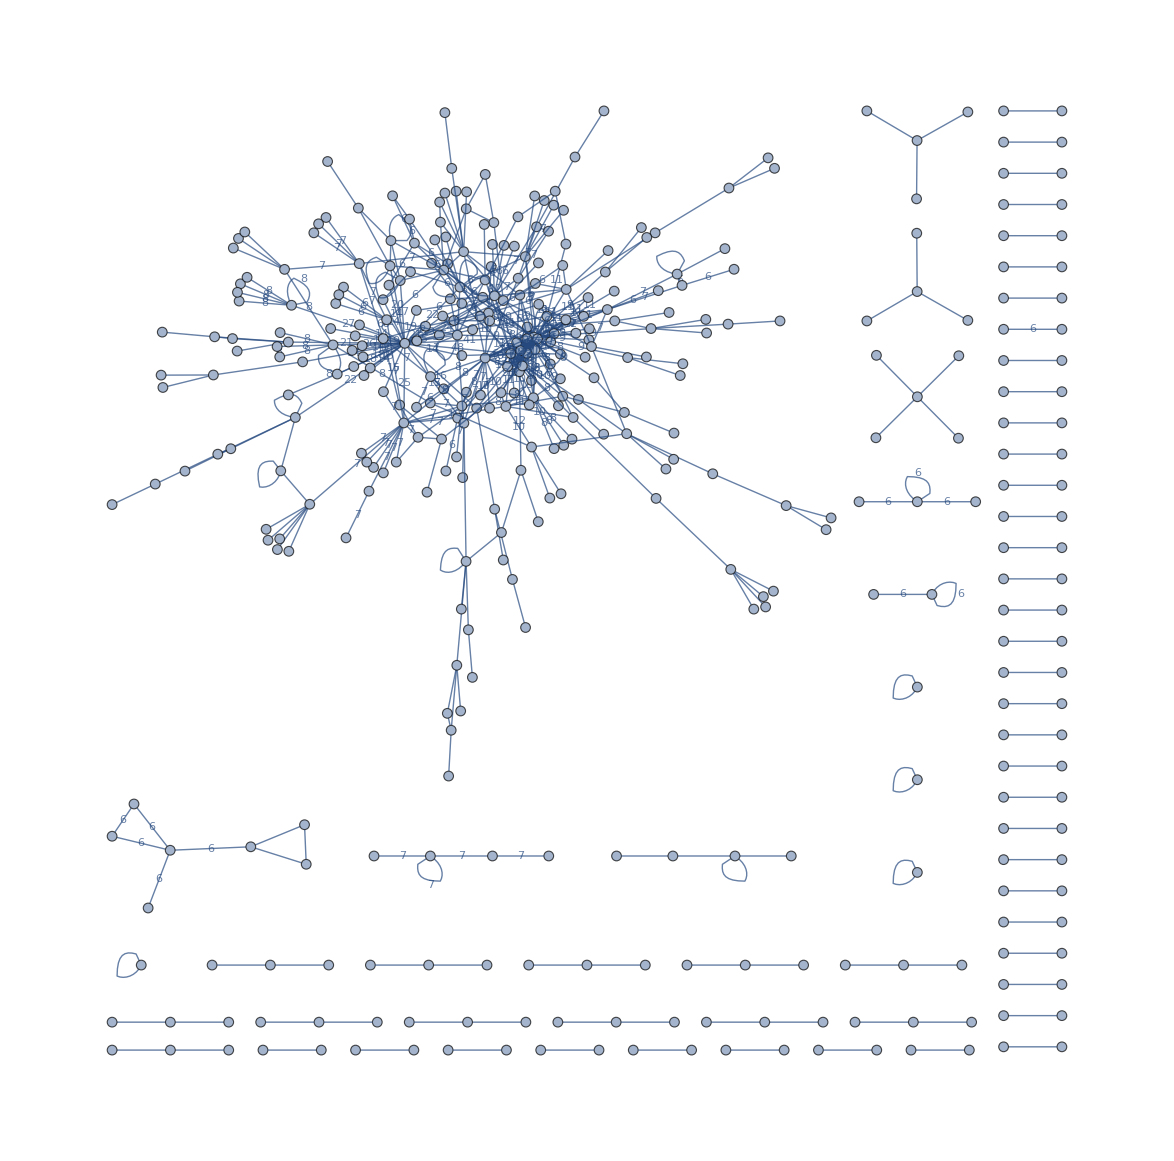

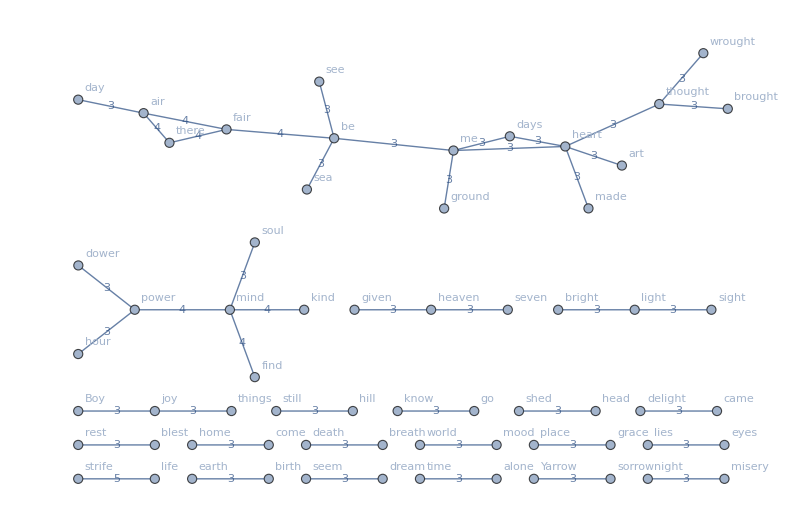

```mathematica
gWeighted4 = UndirectedGraph[cutOrderedPairs,EdgeWeight-> cutOrderedPairsCounts,EdgeLabels->"EdgeWeight", VertexLabels-> "Name",FormatType->StandardForm]
```

```mathematica
ImageCollage[{2->-Graphics-,2->-Graphics-,3->-Graphics-},Background->White ]
```

```mathematica
-Graphics-//Rasterize
```

-Graphics-